```mathematica
Clear[sol,fulsol,dsol,yf,tDe,yDe,yPDe,vDe,sgnvDe,p0De,parameters,intime,trfa,times,tgrps,fk,fb,l0,ldev,kk,b,m,speedD,leq,mV,bV,stepfreq,steplength,energy,seeds];

nE=3;

Subscript[yf, 1]=1;
Subscript[tDe, 1]=0;
Subscript[yDe, 1]=0;
Subscript[yPDe, 1]=0;

period=200Pi;

parameters={l0->0.4,ϕ->0.7};


Table[{Subscript[leq, k][t]=l0- Cos[ (t-Subscript[tDe, k])],
Subscript[fk, k][t]=(Subscript[leq, k][t]-(y[t]-Subscript[yf, k])),
solutions={};
seeds=Table[i,{i,Subscript[tDe, k]+2,Subscript[tDe, k]+period,1}];
Subscript[sol, k]=NDSolve[Evaluate[{y''[t]==ϕ^2  Subscript[fk, k][t],y[Subscript[tDe, k]]==Subscript[yDe, k],y'[Subscript[tDe, k]]==Subscript[yPDe, k]}/.parameters],y[t],{t,Subscript[tDe, k],Subscript[tDe, k]+period}],
Subscript[fulsol, k]=(y[t]/. Subscript[sol, k])[[1]],
Subscript[dsol, k]=D[Subscript[fulsol, k],t],
Subscript[ddsol, k]=D[Subscript[dsol, k],t],

Do[
sol2=Quiet@FindRoot[Subscript[dsol, k]==Subscript[yPDe, k],{t,seed}];
If[Not[Head[sol2]===FindRoot],AppendTo[solutions,sol2]],{seed,seeds}
],

times=Select[t/.solutions,(Subscript[tDe, k]+2)<#<(Subscript[tDe, k]+period)&],
ys=Flatten[(Subscript[dsol, k]/.t->times)],
tf=Table[(ys[[i]]-Subscript[yPDe, k])<10^-6,{i,1,Length[ys]}],

Subscript[tDe, k+1]=Min[DeleteDuplicates[Pick[times,tf]]];
Subscript[yDe, k+1]=Chop[Subscript[fulsol, k]/.t->Subscript[tDe, k+1]/.parameters],
Subscript[yPDe, k+1]=Chop[(Subscript[dsol, k])/.t->Subscript[tDe, k+1]/.parameters],

Subscript[yf, k+1]=Subscript[yf, k]+(Subscript[yDe, k+1]-Subscript[yDe, k])}


,{k,1,nE}];
```

```mathematica
Subscript[tDe, 2]
```

5.23989

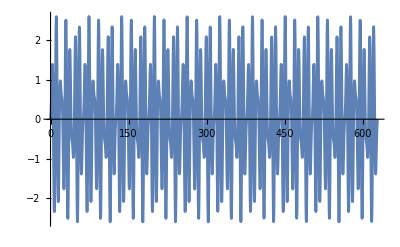

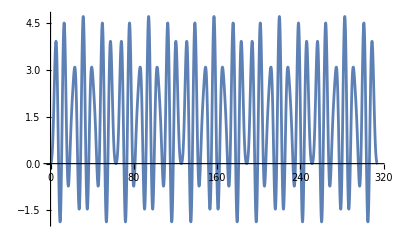

```mathematica
Plot[Subscript[dsol, 1],{t,0,200Pi}]
Plot[Subscript[fulsol, 1],{t,0,100Pi}]
```

```mathematica
tiksfunc[xtiks_]:=Module[{mjtiks,mintiks,joined},
mjtiks=Map[{#,#,0.008}&,xtiks];
mintiks=Flatten[Table[Table[{xtiks[[j]]+i(xtiks[[j+1]]-xtiks[[j]])/(3+1),"",0.004},{i,1,3}],{j,1,Length[xtiks]-1}],1];
joined=Join[mjtiks,mintiks];

joined]

colors=Flatten[Table[{ColorData["AlpineColors",0.1],ColorData["AlpineColors",0.6]},nE]];
colorslimit=f[Flatten[Table[{Subscript[tDe, k]<=t<=Subscript[tDe, k+1],colors[[k]]},{k,1,nE}]]];
colorfunction=Which@@(colorslimit/. List->Sequence);
legends=LineLegend[{ColorData["AlpineColors",0.1],ColorData["AlpineColors",0.5]},{Style["1^st Stance",14,FontFamily->"Latin Modern Math"],Style["2^nd Stance",14,FontFamily->"Latin Modern Math"]},LegendMarkerSize->30,LegendLayout->"Row"];
```

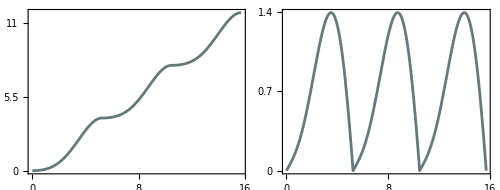

```mathematica
yt=Piecewise[Table[{Subscript[fulsol, i],Subscript[tDe, i]<=t<=Subscript[tDe, i+1]},{i,1,nE+1}]];
yPt=Piecewise[Table[{Subscript[dsol, i],Subscript[tDe, i]<=t<=Subscript[tDe, i+1]},{i,1,nE+1}]];

trplot=Plot[yt,{t,Subscript[tDe, 1],Subscript[tDe, nE+1]},PlotRange->All,Frame->True,FrameLabel->{{MaTeX["\\text{Forward Position, }y"],None},{MaTeX["\\text{Time, }\\tau"],None}},LabelStyle->{Black,14,FontFamily->"Latin Modern Math"},Axes->False,ColorFunction->Function[{t,y},Evaluate[colorfunction]],ColorFunctionScaling->False,FrameTicks->{{tiksfunc[{0,5.5,11}],Automatic},{tiksfunc[{0,8,16}],Automatic}},ImageSize->{230,130},AspectRatio->0.5];
spidplot=Plot[yPt,{t,0,Subscript[tDe, nE+1]},PlotRange->All,Frame->True,FrameLabel->{{MaTeX["\\text{Forward Velocity, $\\dot{y}$}"],None},{MaTeX["\\text{Time, }\\tau"],None}},LabelStyle->{Black,14,FontFamily->"Latin Modern Math"},Axes->False,ColorFunction->Function[{t,y},Evaluate[colorfunction]],ColorFunctionScaling->False,FrameTicks->{{tiksfunc[{0,0.7,1.4}],Automatic},{tiksfunc[{0,8,16}],Automatic}},ImageSize->{220,130},AspectRatio->0.5];
plot=Show[GraphicsGrid[{{legends,SpanFromLeft},{trplot,spidplot}},ImageSize->{500,190},Spacings->{Scaled[-0],Scaled[0]}],
Graphics[Text[Style["a",18,FontFamily->"Latin Modern Math"],{15,-30}]],Graphics[Text[Style["b",18,FontFamily->"Latin Modern Math"],{240,-32}]],FontFamily->"Latin Modern Math"]
```

```mathematica
Export["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Figures\\1Dgait.pdf",plot]
```

C:\Users\by2475\Dropbox\NYU POSTDOC DRIVE\Ants Project\Mathematica\2D model\Updated Figures\1Dgait.pdf

```mathematica
massP=Piecewise[Table[{{1,Subscript[fulsol, k]},Subscript[tDe, k]<=t<=Subscript[tDe, k+1]},{k,1,nE}]];
footP=Piecewise[Table[{{1,Subscript[yf, k]},Subscript[tDe, k]<=t<=Subscript[tDe, k+1]},{k,1,nE}]];
```

```mathematica
colors=Flatten[Table[{RGBColor[0.9,0.6,0.1],RGBColor[0.5,0.1,0.6]},nE]];
colorslimit=f[Flatten[Table[{Subscript[tDe, k]<=t<=Subscript[tDe, k+1],colors[[k]]},{k,1,nE}]]];
colorfunction=Which@@(colorslimit/. List->Sequence);


animie=Manipulate[Show[Graphics[{Thick,(colorfunction/.t->time),Line[{massP,footP}/.t->time]},PlotRange->{{0,2},{-1,Subscript[yDe, nE+1]+1}},Frame->True,LabelStyle->{Black,14},AspectRatio->0.8,FrameLabel->{{"Normalized Forward Position",None},{"Normalized Lateral Position",None}}],
Graphics[{PointSize[0.02],Point[massP/.t->time]}]],{time,Subscript[tDe, 1],Subscript[tDe, nE+1],0.005,Appearance->"Labeled",ControlPlacement->Top},Bookmarks->{"start":>(time=0+10^-6),"end":>(time=Subscript[tDe, nE+1])}]
```

Select::normal: Nonatomic expression expected at position 1 in Select[t,tDe_k+2<#1<tDe_k+period&].

Pick::incomp: Expressions Select[t,tDe_k+2<#1<tDe_k+period&] and {-0.5+Select[t,Subscript[«2»]+2<#1<Subscript[«2»]+period&]<1/1000000} have incompatible shapes.

```mathematica
Export["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Figures\\1Dgait.mp4",animie,"AnimationDuration"->6,FrameRate->15]
```

C:\Users\by2475\Dropbox\NYU POSTDOC DRIVE\Ants Project\Mathematica\2D model\Updated Figures\1Dgait.mp4

## Function to Process points

```mathematica
closedranges[speedFreq_,speedstride_,freqEQ_,strideEQ_,npoints_]:=Module[{distances,first50closed,positioncloset,positioncloset2,speedrange,freqrange,distances2,first50closet2,speedrange2,freqrange2,positionF,speedfreqcloset,speedstridecloset,speedFC,speedSC,expfreq,expstride,thfreq,thstride,perdiffFreq,perdiffstride},

freqFunc[t]=freqEQ;
distances=Table[EuclideanDistance[speedFreq[[i]],{speedFreq[[i,1]],(freqFunc[t]/.t-> speedFreq[[i,1]] )}],{i,1,Length[speedFreq]}];
first50closed=Sort[distances][[;;npoints]];
positioncloset=Table[Position[distances,first50closed[[i]]],{i,1,Length[first50closed]}]//Flatten;
speedrange=Sort[Map[#[[1]]&,speedFreq[[positioncloset]]]];
freqrange=Sort[Map[#[[2]]&,speedFreq[[positioncloset]]]];


strideFunc[t]=strideEQ;
distances2=Table[EuclideanDistance[speedstride[[i]],{speedstride[[i,1]],(strideFunc[t]/.t->speedstride[[i,1]] )}],{i,1,Length[speedstride]}];
first50closet2=Sort[distances2][[;;npoints]];
positioncloset2=Table[Position[distances2,first50closet2[[i]]],{i,1,Length[first50closet2]}]//Flatten;
speedrange2=Sort[Map[#[[1]]&,speedstride[[positioncloset2]]]];
freqrange2=Sort[Map[#[[2]]&,speedstride[[positioncloset2]]]];
positionF=DeleteDuplicates[Join[positioncloset,positioncloset2]];

speedfreqcloset=speedFreq[[positioncloset]];
speedstridecloset=speedstride[[positioncloset2]];
speedFC=Map[First,speedfreqcloset];
speedSC=Map[First,speedstridecloset];
expfreq=freqFunc[t]/.t->speedFC;
expstride=strideFunc[t]/.t->speedSC;
thfreq=Map[Last,speedfreqcloset];
thstride=Map[Last,speedstridecloset];
perdiffFreq=Abs[((expfreq-thfreq)/expfreq)*100];
perdiffstride=Abs[((expstride-thstride)/expstride)*100];

{MinMax[perdiffFreq],MinMax[perdiffstride],MinMax[speedrange],MinMax[freqrange],MinMax[speedrange2],MinMax[freqrange2]}]
```

## Plot Function

```mathematica
plotfunc[speedFreq_,yaxislabel_,xaxislabel_,yaxistiks_,xaxistiks_,eq_,eqstring_,eqpos_,trange_]:=Show[ListPlot[speedFreq, PlotStyle->{Black,PointSize[0.006]}, Frame -> True, LabelStyle -> {Black, 18,FontFamily->"Latin Modern Math"}, FrameLabel -> {{yaxislabel, None}, {xaxislabel, None}}, PlotRange -> All, ImageSize->{300,260},FrameTicks->{{tiksfunc[yaxistiks],Automatic},{tiksfunc[xaxistiks],Automatic}},Axes->False],
 Plot[eq, trange, PlotStyle -> ColorData["FuchsiaTones", 0.5], PlotRange -> All],
HighlightMesh[ConvexHullMesh[speedFreq],{Style[2,Black,Opacity[0.1]],Style[1,Black,Opacity[1]]}],PlotRange->All
]

tiksfunc[xtiks_]:=Module[{mjtiks,mintiks,joined},
mjtiks=Map[{#,#,0.015}&,xtiks];
mintiks=Flatten[Table[Table[{xtiks[[j]]+i(xtiks[[j+1]]-xtiks[[j]])/(3+1),"",0.004},{i,1,3}],{j,1,Length[xtiks]-1}],1];
joined=Join[mjtiks,mintiks];

joined]

plotfuncComp[relations_,tiksy_,tiksx_,ylabel_,xlabel_,eq_,eqrange_]:=Show[ListPlot[relations,Frame->True,LabelStyle->{Black,16,FontFamily->"Latin Modern Math"},ImageSize->{300,260},PlotStyle->{Black,PointSize[0.006]},FrameTicks->{{tiksfunc[tiksy],Automatic},{tiksfunc[tiksx],Automatic}},FrameLabel->{{ylabel,None},{xlabel,None}},Axes->False],
Plot[eq,eqrange,PlotStyle->ColorData["FuchsiaTones",0.5],PlotRange->All],HighlightMesh[ConvexHullMesh[relations],{Style[2,Black,Opacity[0.1]],Style[1,Black,Opacity[1]]},Axes->False],PlotRange->All
]

plotfuncCompfreq[relations_,tiksy_,tiksx_,ylabel_,xlabel_,eq_,eqrange_]:=Show[ListPlot[relations,Frame->True,LabelStyle->{Black,16,FontFamily->"Latin Modern Math"},ImageSize->{300,260},PlotStyle->{Black,PointSize[0.006]},FrameTicks->{{tiksfunc[tiksy],Automatic},{tiksfunc[tiksx],Automatic}},FrameLabel->{{ylabel,None},{xlabel,None}}],
Plot[eq,eqrange,PlotStyle->ColorData["FuchsiaTones",0.5],PlotRange->All],HighlightMesh[ConvexHullMesh[relations],{Style[2,Black,Opacity[0.1]],Style[1,Black,Opacity[1]]}],PlotRange->{{0,1000},{0,500}}
]
```

## SpeedRelations

```mathematica
speedRelation[specieMax_,ω0_]:=Module[{speedD,stridelength,speedstride,stridefreq,speedfreq,ht,htCb,maxTriLen},
maxTriLen=Table[Table[If[steplengthD[[j,i]]<1,steplengthD[[j,i]],Max[steplengthD[[j,i]]-1,1]],{i,1,nE2}],{j,1,nE3}];
ht=(maxTriLen)/Max[maxTriLen];
htCb=ht*specieMax;
speedD=Flatten[Table[(speed*htCb)[[i]]ω0/mV,{i,1,nE3}]];
stridelength=Flatten[htCb];
speedstride=Transpose[{speedD,stridelength}];
stridefreq=Flatten[Table[(ω0/mV)stepfreqD[[i]],{i,1,nE3}]];
speedfreq=Transpose[{speedD,stridefreq}];
{speedstride,speedfreq}]
```

## AntsEquation

```mathematica
cataglyphisFortisStride=(0.02 t+6.04)/2;
cataglyphisFortisFreq=(0.81 t^0.59)*2;

cataglyphisBicolorStride=(0.02 t +8.18)/2;
cataglyphisBicolorFreq=(10.16 Log[t]-36.02)*2;

cataglyphisAlbicansStride=(0.01 t +5.75)/2;
cataglyphisAlbicansFreq=(0.11t+2.85)*2;

cataglyphisBombycinaStride=(0.02 t +4.72)/2;
cataglyphisBombycinaFreq=(1.43 t^0.52)*2;

formicaPolyctenaStride=0.48 t +4.1;
formicaPolyctenaFreq=0.34 t +7.6;
```

## y 0.5

```mathematica
Clear[sol,fulsol,dsol,yf,tDe,yDe,yPDe,vDe,sgnvDe,p0De,parameters,intime,trfa,times,tgrps,fk,fb,l0,ldev,kk,b,m,speedD,leq,mV,bV,stepfreq,steplength,energy];
```

```mathematica
mV=Table[i,{i,0.01,1,0.02}];
nE2=Length[mV];


l0V=Table[i,{i,0,1,0.1}];
nE3=Length[l0V];
```

### Code

```mathematica
nE=1;

Subscript[yf, 1]=1;
Subscript[tDe, 1]=0;
Subscript[yDe, 1]=0;
Subscript[yPDe, 1]=0.5;

period=200Pi;

Table[Table[{parameters={l0->l0V[[nldev]],ϕ->mV[[nm]]},


Table[{Subscript[leq, k][t]=l0- Cos[ (t-Subscript[tDe, k])],
Subscript[fk, k][t]=(Subscript[leq, k][t]-(y[t]-Subscript[yf, k])),
solutions={};
seeds=Table[i,{i,Subscript[tDe, k]+2,Subscript[tDe, k]+period,2}];
Subscript[sol, k]=NDSolve[Evaluate[{y''[t]==ϕ^2  Subscript[fk, k][t],y[Subscript[tDe, k]]==Subscript[yDe, k],y'[Subscript[tDe, k]]==Subscript[yPDe, k]}/.parameters],y[t],{t,Subscript[tDe, k],Subscript[tDe, k]+period}],
Subscript[fulsol, k]=(y[t]/. Subscript[sol, k])[[1]],
Subscript[dsol, k]=D[Subscript[fulsol, k],t],
Subscript[ddsol, k]=D[Subscript[dsol, k],t],
i=1,
While[Length[solutions]<20&&i<Length[seeds],
sol2=Quiet@FindRoot[Subscript[dsol, k]==Subscript[yPDe, k],{t,seeds[[i]]}];
If[Not[Head[sol2]===FindRoot],AppendTo[solutions,sol2]];
i++;
],

times=Select[t/.solutions,(Subscript[tDe, k]+2)<#<(Subscript[tDe, k]+period)&],
ys=Flatten[(Subscript[dsol, k]/.t->times)],
tf=Table[(ys[[i]]-Subscript[yPDe, k])<10^-6,{i,1,Length[ys]}],

Subscript[tDe, k+1]=Min[DeleteDuplicates[Pick[times,tf]]];
Subscript[yDe, k+1]=Chop[Subscript[fulsol, k]/.t->Subscript[tDe, k+1]/.parameters],
Subscript[yPDe, k+1]=Chop[(Subscript[dsol, k])/.t->Subscript[tDe, k+1]/.parameters],

Subscript[yf, k+1]=Subscript[yf, k]+(Subscript[yDe, k+1]-Subscript[yDe, k])}


,{k,1,nE}],
Subscript[speedD, nm,nldev]=(Subscript[yDe, nE+1]-Subscript[yDe, 1])/Subscript[tDe, nE+1],
Subscript[stepfreq, nm,nldev]=1/{Subscript[tDe, nE+1]-Subscript[tDe, nE]},
Subscript[steplength, nm,nldev]=Subscript[yDe, nE+1]-Subscript[yDe, nE],
Subscript[energy, nm,nldev]=NIntegrate[Abs[(Subscript[leq, nE][t]-(Subscript[fulsol, nE]-Subscript[yf, nE]))(D[Subscript[leq, nE][t],t])/.parameters],{t,Subscript[tDe, nE],Subscript[tDe, nE+1]},PrecisionGoal->3],
Subscript[grf, nm,nldev]=Max[First[FindMaximum[(Subscript[leq, nE][t]-(Subscript[fulsol, nE]-Subscript[yf, nE]))/.parameters,{t,Subscript[tDe, nE],Subscript[tDe, nE+1]}]],
Abs[First[FindMinimum[(Subscript[leq, nE][t]-(Subscript[fulsol, nE]-Subscript[yf, nE]))/.parameters,{t,Subscript[tDe, nE+1],Subscript[tDe, nE]}]]]]

},{nm,1,nE2}],{nldev,1,nE3}];
```

InterpolatingFunction::dmval: Input value {-0.0931667} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.745333} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.342272} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
speed=Table[Table[Subscript[speedD, nm,nldev],{nm,1,nE2}],{nldev,1,nE3}];
steplengthD=Table[Table[Subscript[steplength, nm,nldev],{nm,1,nE2}],{nldev,1,nE3}];
stepfreqD=Table[Flatten[Table[Subscript[stepfreq, nm,nldev],{nm,1,nE2}]],{nldev,1,nE3}];
energyD=Table[Flatten[Table[Subscript[energy, nm,nldev],{nm,1,nE2}]],{nldev,1,nE3}];
gRFmax=Table[Flatten[Table[Subscript[grf, nm,nldev],{nm,1,nE2}]],{nldev,1,nE3}];
effic=0.5 speed^2/energyD*100;
cot=energyD/steplengthD;
```

### Import export

```mathematica
Export["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Code2\\1D model\\speedY2.mx",speed];
Export["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Code2\\1D model\\steplengthDY2.mx",steplengthD];
Export["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Code2\\1D model\\stepfreqDY2.mx",stepfreqD];
Export["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Code2\\1D model\\energyDY2.mx",energyD];
Export["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Code2\\1D model\\grfmaxY2.mx",gRFmax];
Export["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Code2\\1D model\\efficY2.mx",effic];
Export["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Code2\\1D model\\cotY2.mx",cot];
```

```mathematica
speed=Import["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Code2\\1D model\\speedY2.mx"];
steplengthD=Import["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Code2\\1D model\\steplengthDY2.mx"];
stepfreqD=Import["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Code2\\1D model\\stepfreqDY2.mx"];
energyD=Import["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Code2\\1D model\\energyDY2.mx"];
gRFmax=Import["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Code2\\1D model\\grfmaxY2.mx"];
effic=Import["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Code2\\1D model\\efficY2.mx"];
cot=Import["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Code2\\1D model\\cotY2.mx"];
```

### Cataglyphis Bicolor

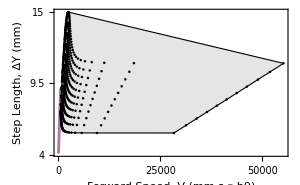

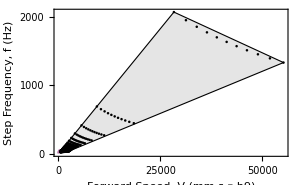

```mathematica
relations=speedRelation[15,100];
p5Cb1=plotfuncComp[relations[[1]],{4,9.5,15},{0,25000,50000},"Step Length, ΔY (mm)","Forward Forward Forward Forward Speed, V (mm s ⁻.b9)",cataglyphisBicolorStride,{t,0,500}]
p5Cb2=plotfuncComp[relations[[2]],{0,1000,2000},{0,25000,50000},"Step Frequency, f (Hz)","Forward Forward Forward Forward Speed, V (mm s ⁻.b9)",cataglyphisBicolorFreq,{t,40,500}]
```

```mathematica
closedranges[relations[[2]],relations[[1]],cataglyphisBicolorFreq,cataglyphisBicolorStride,200]
```

{{0.535835,55.0135},{20.2654,54.5339},{514.332,5463.95},{24.6594,131.484},{514.332,1661.99},{6.0573,13.6011}}

### Cataglyphis Albicans

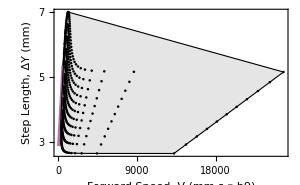

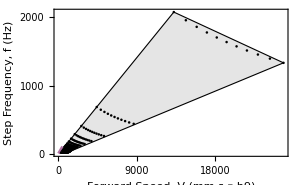

```mathematica
relations=speedRelation[7,100];
p5Ca1=plotfuncComp[relations[[1]],{3,5,7},{0,9000,18000},"Step Length, ΔY (mm)","Forward Forward Forward Forward Speed, V (mm s ⁻.b9)",cataglyphisAlbicansStride,{t,0,500}]
p5Ca2=plotfuncComp[relations[[2]],{0,1000,2000},{0,9000,18000},"Step Frequency, f (Hz)","Forward Forward Forward Forward Speed, V (mm s ⁻.b9)",cataglyphisAlbicansFreq,{t,40,500}]
```

```mathematica
closedranges[relations[[2]],relations[[1]],cataglyphisAlbicansFreq,cataglyphisAlbicansStride,20]
```

{{49.1632,57.8506},{5.42929,8.0346},{240.022,300.718},{24.6594,36.5303},{398.84,775.595},{4.49167,6.34718}}

### Cataglyphis Fortis

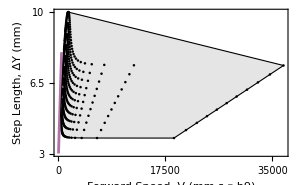

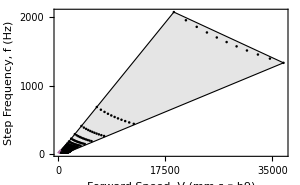

```mathematica
relations=speedRelation[10,100];
p5Cf1=plotfuncComp[relations[[1]],{3,6.5,10},{0,17500,35000},"Step Length, ΔY (mm)","Forward Forward Forward Forward Speed, V (mm s ⁻.b9)",cataglyphisFortisStride,{t,0,500}]
p5Cf2=plotfuncComp[relations[[2]],{0,1000,2000},{0,17500,35000},"Step Frequency, f (Hz)","Forward Forward Forward Forward Speed, V (mm s ⁻.b9)",cataglyphisFortisFreq,{t,40,500}]
```

```mathematica
closedranges[relations[[2]],relations[[1]],cataglyphisFortisFreq,cataglyphisFortisStride,20]
```

{{0.247174,9.96176},{23.8922,29.5516},{677.209,6641.25},{68.2446,292.781},{342.888,468.231},{4.74308,5.66704}}

### Formica Polyctena

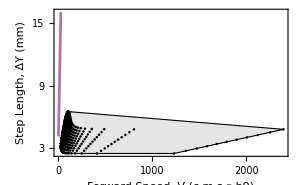

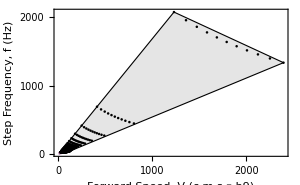

```mathematica
relations=speedRelation[6.5,100];
p5fp1=plotfuncComp[{#[[1]]/10,#[[2]]}&/@relations[[1]],{3,9,15},{0,1000,2000},"Step Length, ΔY (mm)","Forward Speed, V (c m s ⁻.b9)",formicaPolyctenaStride,{t,0,25}]
p5fp2=plotfuncComp[{#[[1]]/10,#[[2]]}&/@relations[[2]],{0,1000,2000},{0,1000,2000},"Step Frequency, f (Hz)","Forward Speed, V (c m s ⁻.b9)",formicaPolyctenaFreq,{t,0,50}]
```

```mathematica
closedranges[relations[[2]],relations[[1]],formicaPolyctenaFreq,formicaPolyctenaStride,20]
```

{{64.3749,70.4246},{97.128,97.7263},{222.877,279.238},{24.6594,36.5303},{222.877,264.922},{2.95876,3.42035}}

### Cataglyphis bombycina

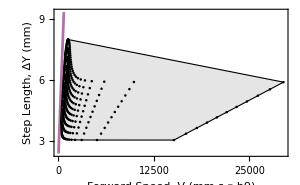

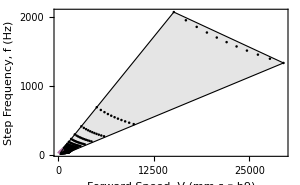

```mathematica
relations=speedRelation[8,100];
p5Cbm1=plotfuncComp[relations[[1]],{3,6,9},{0,12500,25000},"Step Length, ΔY (mm)","Forward Forward Forward Forward Speed, V (mm s ⁻.b9)",cataglyphisBombycinaStride,{t,0,700}]
p5Cbm2=plotfuncComp[relations[[2]],{0,1000,2000},{0,12500,25000},"Step Frequency, f (Hz)","Forward Forward Forward Forward Speed, V (mm s ⁻.b9)",cataglyphisBombycinaFreq,{t,40,700}]
```

```mathematica
closedranges[relations[[2]],relations[[1]],cataglyphisBombycinaFreq,cataglyphisBombycinaStride,20]
```

{{94.6551,95.8947},{29.1637,36.2277},{224.929,288.324},{0.981167,1.45349},{224.929,360.597},{6.21673,8.3823}}

## y 0.1

### code

```mathematica
Clear[sol,fulsol,dsol,yf,tDe,yDe,yPDe,vDe,sgnvDe,p0De,parameters,intime,trfa,times,tgrps,fk,fb,l0,ldev,kk,b,m,speedD,leq,mV,bV,stepfreq,steplength,energy];

nE=1;

Subscript[yf, 1]=1;
Subscript[tDe, 1]=0;
Subscript[yDe, 1]=0;
Subscript[yPDe, 1]=0.1;

mV=Table[i,{i,0.01,1,0.02}];
nE2=Length[mV];


l0V=Table[i,{i,0,1,0.1}];
nE3=Length[l0V];

period=200Pi;

Table[Table[{parameters={l0->l0V[[nldev]],ϕ->mV[[nm]]},


Table[{Subscript[leq, k][t]=l0- Cos[ (t-Subscript[tDe, k])],
Subscript[fk, k][t]=(Subscript[leq, k][t]-(y[t]-Subscript[yf, k])),
solutions={};
seeds=Table[i,{i,Subscript[tDe, k]+2,Subscript[tDe, k]+period,2}];
Subscript[sol, k]=NDSolve[Evaluate[{y''[t]==ϕ^2  Subscript[fk, k][t],y[Subscript[tDe, k]]==Subscript[yDe, k],y'[Subscript[tDe, k]]==Subscript[yPDe, k]}/.parameters],y[t],{t,Subscript[tDe, k],Subscript[tDe, k]+period}],
Subscript[fulsol, k]=(y[t]/. Subscript[sol, k])[[1]],
Subscript[dsol, k]=D[Subscript[fulsol, k],t],
Subscript[ddsol, k]=D[Subscript[dsol, k],t],
i=1,
While[Length[solutions]<20&&i<Length[seeds],
sol2=Quiet@FindRoot[Subscript[dsol, k]==Subscript[yPDe, k],{t,seeds[[i]]}];
If[Not[Head[sol2]===FindRoot],AppendTo[solutions,sol2]];
i++;
],

times=Select[t/.solutions,(Subscript[tDe, k]+2)<#<(Subscript[tDe, k]+period)&],
ys=Flatten[(Subscript[dsol, k]/.t->times)],
tf=Table[(ys[[i]]-Subscript[yPDe, k])<10^-6,{i,1,Length[ys]}],

Subscript[tDe, k+1]=Min[DeleteDuplicates[Pick[times,tf]]];
Subscript[yDe, k+1]=Chop[Subscript[fulsol, k]/.t->Subscript[tDe, k+1]/.parameters],
Subscript[yPDe, k+1]=Chop[(Subscript[dsol, k])/.t->Subscript[tDe, k+1]/.parameters],

Subscript[yf, k+1]=Subscript[yf, k]+(Subscript[yDe, k+1]-Subscript[yDe, k])}


,{k,1,nE}],
Subscript[speedD, nm,nldev]=(Subscript[yDe, nE+1]-Subscript[yDe, 1])/Subscript[tDe, nE+1],
Subscript[stepfreq, nm,nldev]=1/{Subscript[tDe, nE+1]-Subscript[tDe, nE]},
Subscript[steplength, nm,nldev]=Subscript[yDe, nE+1]-Subscript[yDe, nE],
Subscript[energy, nm,nldev]=NIntegrate[Abs[(Subscript[leq, nE][t]-(Subscript[fulsol, nE]-Subscript[yf, nE]))(D[Subscript[leq, nE][t],t])/.parameters],{t,Subscript[tDe, nE],Subscript[tDe, nE+1]},PrecisionGoal->3],
Subscript[grf, nm,nldev]=Max[First[FindMaximum[(Subscript[leq, nE][t]-(Subscript[fulsol, nE]-Subscript[yf, nE]))/.parameters,{t,Subscript[tDe, nE],Subscript[tDe, nE+1]}]],
Abs[First[FindMinimum[(Subscript[leq, nE][t]-(Subscript[fulsol, nE]-Subscript[yf, nE]))/.parameters,{t,Subscript[tDe, nE+1],Subscript[tDe, nE]}]]]]

},{nm,1,nE2}],{nldev,1,nE3}];
```

$Aborted

```mathematica
tdata=Table[i,{i,0,1,1/(4-1)}];
tydata=Table[i,{i,0,1,1/(3-1)}];
mjtkxdata=Table[i,{i,Min[mV],Max[mV],(Max[mV]-Min[mV])/(4-1)}];

ticksx=Table[{tdata[[Position[mjtkxdata,i][[1,1]]]],i,0.02},{i,mjtkxdata}];
mjtkx=Join[{ticksx[[1]]},Round[Rest[Most[ticksx]],0.01],{Round[Last[ticksx],0.01]}];


mjtkydata=Table[i,{i,Min[l0V],Max[l0V],(Max[l0V]-Min[l0V])/(3-1)}];


ticksy=Table[{tydata[[Position[mjtkydata,i][[1,1]]]],i,0.02},{i,mjtkydata}];
mjtky=Join[{ticksy[[1]]},Round[Rest[Most[ticksy]],0.01],{Round[Last[ticksy],0.01]}];

mtk=Table[{i,"",0.01},{i,0,1,1/(9-1)}];


speed=Table[Table[Subscript[speedD, nm,nldev],{nm,1,nE2}],{nldev,1,nE3}];
steplengthD=Table[Table[Subscript[steplength, nm,nldev]*2,{nm,1,nE2}],{nldev,1,nE3}];
stepfreqD=Table[Flatten[Table[Subscript[stepfreq, nm,nldev]/2,{nm,1,nE2}]],{nldev,1,nE3}];
energyD=Table[Flatten[Table[Subscript[energy, nm,nldev],{nm,1,nE2}]],{nldev,1,nE3}];
gRFmax=Table[Flatten[Table[Subscript[grf, nm,nldev],{nm,1,nE2}]],{nldev,1,nE3}];
effic=0.5 speed^2/energyD*100;
cot=energyD/steplengthD;
```

### import export

```mathematica
Export["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Code2\\1D model\\speedY1.mx",speed];
Export["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Code2\\1D model\\steplengthDY1.mx",steplengthD];
Export["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Code2\\1D model\\stepfreqDY1.mx",stepfreqD];
Export["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Code2\\1D model\\energyDY1.mx",energyD];
Export["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Code2\\1D model\\grfmaxY1.mx",gRFmax];
Export["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Code2\\1D model\\efficY1.mx",effic];
Export["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Code2\\1D model\\cotY1.mx",cot];
```

```mathematica
speed=Import["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Code2\\1D model\\speedY1.mx"];
steplengthD=Import["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Code2\\1D model\\steplengthDY1.mx"];
stepfreqD=Import["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Code2\\1D model\\stepfreqDY1.mx"];
energyD=Import["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Code2\\1D model\\energyDY1.mx"];
gRFmax=Import["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Code2\\1D model\\grfmaxY1.mx"];
effic=Import["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Code2\\1D model\\efficY1.mx"];
cot=Import["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Code2\\1D model\\cotY1.mx"];
```

### Cataglyphis Bicolor

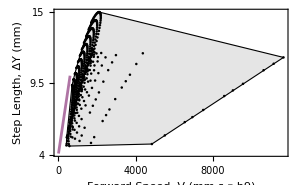

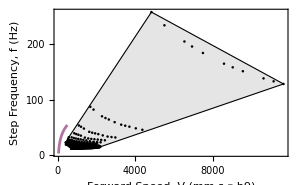

```mathematica
relations=speedRelation[15,100];
p1Cb1=plotfuncComp[relations[[1]],{4,9.5,15},{0,4000,8000},"Step Length, ΔY (mm)","Forward Speed, V (mm s ⁻.b9)",cataglyphisBicolorStride,{t,0,600}]
p1Cb2=plotfuncComp[relations[[2]],{0,100,200},{0,4000,8000},"Step Frequency, f (Hz)","Forward Speed, V (mm s ⁻.b9)",cataglyphisBicolorFreq,{t,40,500}]
```

```mathematica
closedranges[relations[[2]],relations[[1]],cataglyphisBicolorFreq,cataglyphisBicolorStride,200]
```

{{1.48863,81.8258},{15.7648,49.0893},{408.682,11655.4},{11.3356,158.173},{408.682,1345.87},{4.71388,12.7026}}

### Cataglyphis Albicans

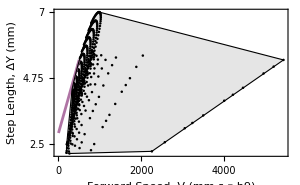

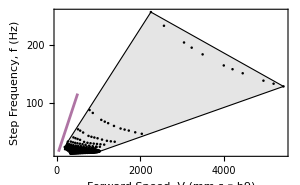

```mathematica
relations=speedRelation[7,100];
p1Ca1=plotfuncComp[relations[[1]],{2.5,4.75,7},{0,2000,4000},"Step Length, ΔY (mm)","Forward Speed, V (mm s ⁻.b9)",cataglyphisAlbicansStride,{t,0,500}]
p1Ca2=plotfuncComp[relations[[2]],{0,100,200},{0,2000,4000},"Step Frequency, f (Hz)","Forward Speed, V (mm s ⁻.b9)",cataglyphisAlbicansFreq,{t,40,500}]
```

```mathematica
closedranges[relations[[2]],relations[[1]],cataglyphisAlbicansFreq,cataglyphisAlbicansStride,20]
```

{{89.347,93.5138},{11.5126,16.2286},{137.99,191.471},{1.45967,2.54732},{354.791,672.186},{7.84314,10.9296}}

### Cataglyphis Fortis

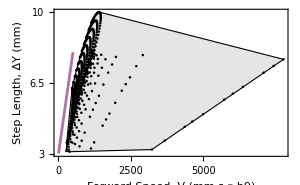

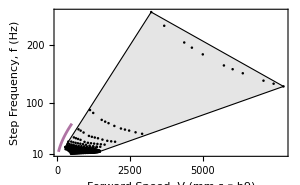

```mathematica
relations=speedRelation[10,100];
p1Cf1=plotfuncComp[relations[[1]],{3,6.5,10},{0,2500,5000},"Step Length, ΔY (mm)","Forward Forward Speed, V (mm s ⁻.b9)",cataglyphisFortisStride,{t,0,500}]
p1Cf2=plotfuncComp[relations[[2]],{10,100,200},{0,2500,5000},"Step Frequency, f (Hz)","Forward Forward Speed, V (mm s ⁻.b9)",cataglyphisFortisFreq,{t,40,500}]
```

```mathematica
closedranges[relations[[2]],relations[[1]],cataglyphisFortisFreq,cataglyphisFortisStride,20]
```

{{9.9677,58.7298},{18.9721,24.5196},{272.455,4360.14},{18.8987,233.9},{468.391,579.153},{6.02856,6.84272}}

### Formica Polyctena

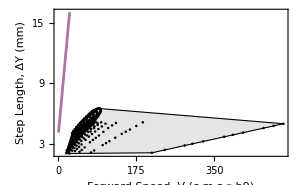

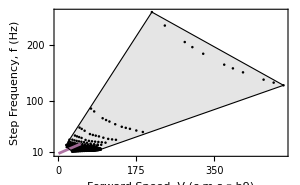

```mathematica
relations=speedRelation[6.5,100];
p1fp1=plotfuncComp[{#[[1]]/10,#[[2]]}&/@relations[[1]],{3,9,15},{0,175,350},"Step Length, ΔY (mm)","Forward Speed, V (c m s ⁻.b9)",formicaPolyctenaStride,{t,0,25}]
p1fp2=plotfuncComp[{#[[1]]/10,#[[2]]}&/@relations[[2]],{10,100,200},{0,175,350},"Step Frequency, f (Hz)","Forward Speed, V (c m s ⁻.b9)",formicaPolyctenaFreq,{t,0,50}]
```

```mathematica
closedranges[relations[[2]],relations[[1]],formicaPolyctenaFreq,formicaPolyctenaStride,20]
```

{{96.2567,97.7204},{95.0716,96.4429},{128.133,177.794},{1.45967,2.54732},{128.133,175.151},{2.95586,3.91989}}

### Cataglyphis bombycina

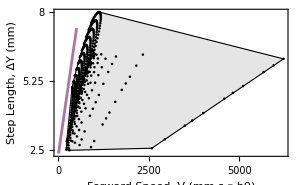

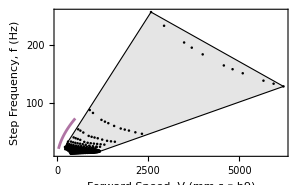

```mathematica
relations=speedRelation[8,100];
p1Cbm1=plotfuncComp[relations[[1]],{2.5,5.25,8},{0,2500,5000},"Step Length, ΔY (mm)","Forward Forward Forward Speed, V (mm s ⁻.b9)",cataglyphisBombycinaStride,{t,0,500}]
p1Cbm2=plotfuncComp[relations[[2]],{0,100,200},{0,2500,5000},"Step Frequency, f (Hz)","Forward Forward Forward Speed, V (mm s ⁻.b9)",cataglyphisBombycinaFreq,{t,40,500}]
```

```mathematica
closedranges[relations[[2]],relations[[1]],cataglyphisBombycinaFreq,cataglyphisBombycinaStride,20]
```

{{2.96877,60.8517},{18.2291,23.8522},{217.964,3997.94},{18.8987,204.747},{374.713,463.322},{4.82285,5.47417}}

## y 0.05

### Code

```mathematica
Clear[sol,fulsol,dsol,yf,tDe,yDe,yPDe,vDe,sgnvDe,p0De,parameters,intime,trfa,times,tgrps,fk,fb,l0,ldev,kk,b,m,speedD,leq,mV,bV,stepfreq,steplength,energy];

nE=1;
mV=Table[i,{i,0.01,1,0.02}];
nE2=Length[mV];


l0V=Table[i,{i,0,1,0.1}];
nE3=Length[l0V];
Subscript[yf, 1]=1;
Subscript[tDe, 1]=0;
Subscript[yDe, 1]=0;
Subscript[yPDe, 1]=0.05;

period=200Pi;

Table[Table[{parameters={l0->l0V[[nldev]],ϕ->mV[[nm]]},


Table[{Subscript[leq, k][t]=l0- Cos[ (t-Subscript[tDe, k])],
Subscript[fk, k][t]=(Subscript[leq, k][t]-(y[t]-Subscript[yf, k])),
solutions={};
seeds=Table[i,{i,Subscript[tDe, k]+2,Subscript[tDe, k]+period,2}];
Subscript[sol, k]=NDSolve[Evaluate[{y''[t]==ϕ^2  Subscript[fk, k][t],y[Subscript[tDe, k]]==Subscript[yDe, k],y'[Subscript[tDe, k]]==Subscript[yPDe, k]}/.parameters],y[t],{t,Subscript[tDe, k],Subscript[tDe, k]+period}],
Subscript[fulsol, k]=(y[t]/. Subscript[sol, k])[[1]],
Subscript[dsol, k]=D[Subscript[fulsol, k],t],
Subscript[ddsol, k]=D[Subscript[dsol, k],t],
i=1,
While[Length[solutions]<20&&i<Length[seeds],
sol2=Quiet@FindRoot[Subscript[dsol, k]==Subscript[yPDe, k],{t,seeds[[i]]}];
If[Not[Head[sol2]===FindRoot],AppendTo[solutions,sol2]];
i++;
],

times=Select[t/.solutions,(Subscript[tDe, k]+2)<#<(Subscript[tDe, k]+period)&],
ys=Flatten[(Subscript[dsol, k]/.t->times)],
tf=Table[(ys[[i]]-Subscript[yPDe, k])<10^-6,{i,1,Length[ys]}],

Subscript[tDe, k+1]=Min[DeleteDuplicates[Pick[times,tf]]];
Subscript[yDe, k+1]=Chop[Subscript[fulsol, k]/.t->Subscript[tDe, k+1]/.parameters],
Subscript[yPDe, k+1]=Chop[(Subscript[dsol, k])/.t->Subscript[tDe, k+1]/.parameters],

Subscript[yf, k+1]=Subscript[yf, k]+(Subscript[yDe, k+1]-Subscript[yDe, k])}


,{k,1,nE}],
Subscript[speedD, nm,nldev]=(Subscript[yDe, nE+1]-Subscript[yDe, 1])/Subscript[tDe, nE+1],
Subscript[stepfreq, nm,nldev]=1/{Subscript[tDe, nE+1]-Subscript[tDe, nE]},
Subscript[steplength, nm,nldev]=Subscript[yDe, nE+1]-Subscript[yDe, nE],
Subscript[energy, nm,nldev]=NIntegrate[Abs[(Subscript[leq, nE][t]-(Subscript[fulsol, nE]-Subscript[yf, nE]))(D[Subscript[leq, nE][t],t])/.parameters],{t,Subscript[tDe, nE],Subscript[tDe, nE+1]},PrecisionGoal->3],
Subscript[grf, nm,nldev]=Max[First[FindMaximum[(Subscript[leq, nE][t]-(Subscript[fulsol, nE]-Subscript[yf, nE]))/.parameters,{t,Subscript[tDe, nE],Subscript[tDe, nE+1]}]],
Abs[First[FindMinimum[(Subscript[leq, nE][t]-(Subscript[fulsol, nE]-Subscript[yf, nE]))/.parameters,{t,Subscript[tDe, nE+1],Subscript[tDe, nE]}]]]]

},{nm,1,nE2}],{nldev,1,nE3}];
```

InterpolatingFunction::dmval: Input value {-0.084951} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.137454} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.222405} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
tdata=Table[i,{i,0,1,1/(4-1)}];
tydata=Table[i,{i,0,1,1/(3-1)}];
mjtkxdata=Table[i,{i,Min[mV],Max[mV],(Max[mV]-Min[mV])/(4-1)}];

ticksx=Table[{tdata[[Position[mjtkxdata,i][[1,1]]]],i,0.02},{i,mjtkxdata}];
mjtkx=Join[{ticksx[[1]]},Round[Rest[Most[ticksx]],0.01],{Round[Last[ticksx],0.01]}];


mjtkydata=Table[i,{i,Min[l0V],Max[l0V],(Max[l0V]-Min[l0V])/(3-1)}];


ticksy=Table[{tydata[[Position[mjtkydata,i][[1,1]]]],i,0.02},{i,mjtkydata}];
mjtky=Join[{ticksy[[1]]},Round[Rest[Most[ticksy]],0.01],{Round[Last[ticksy],0.01]}];

mtk=Table[{i,"",0.01},{i,0,1,1/(9-1)}];


speed=Table[Table[Subscript[speedD, nm,nldev],{nm,1,nE2}],{nldev,1,nE3}];
steplengthD=Table[Table[Subscript[steplength, nm,nldev]*2,{nm,1,nE2}],{nldev,1,nE3}];
stepfreqD=Table[Flatten[Table[Subscript[stepfreq, nm,nldev]/2,{nm,1,nE2}]],{nldev,1,nE3}];
energyD=Table[Flatten[Table[Subscript[energy, nm,nldev],{nm,1,nE2}]],{nldev,1,nE3}];
gRFmax=Table[Flatten[Table[Subscript[grf, nm,nldev],{nm,1,nE2}]],{nldev,1,nE3}];
effic=0.5 speed^2/energyD*100;
cot=energyD/steplengthD;
```

### import export

```mathematica
Export["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Code2\\1D model\\speedY05.mx",speed];
Export["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Code2\\1D model\\steplengthDY05.mx",steplengthD];
Export["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Code2\\1D model\\stepfreqDY05.mx",stepfreqD];
Export["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Code2\\1D model\\energyDY05.mx",energyD];
Export["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Code2\\1D model\\grfmaxY05.mx",gRFmax];
Export["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Code2\\1D model\\efficY05.mx",effic];
Export["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Code2\\1D model\\cotY05.mx",cot];
```

```mathematica
speed=Import["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Code2\\1D model\\speedY05.mx"];
steplengthD=Import["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Code2\\1D model\\steplengthDY05.mx"];
stepfreqD=Import["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Code2\\1D model\\stepfreqDY05.mx"];
energyD=Import["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Code2\\1D model\\energyDY05.mx"];
gRFmax=Import["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Code2\\1D model\\grfmaxY05.mx"];
effic=Import["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Code2\\1D model\\efficY05.mx"];
cot=Import["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Code2\\1D model\\cotY05.mx"];
```

### Cataglyphis Bicolor

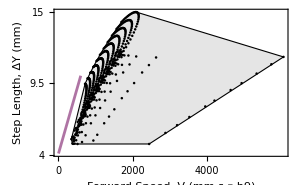

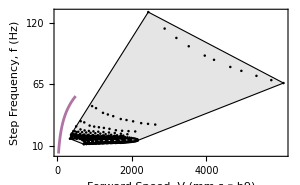

```mathematica
relations=speedRelation[15,100];
p05Cb1=plotfuncComp[relations[[1]],{4,9.5,15},{0,2000,4000},"Step Length, ΔY (mm)","Forward Speed, V (mm s ⁻.b9)",cataglyphisBicolorStride,{t,0,600}]
p05Cb2=plotfuncComp[relations[[2]],{10,65,120},{0,2000,4000},"Step Frequency, f (Hz)","Forward Speed, V (mm s ⁻.b9)",cataglyphisBicolorFreq,{t,40,500}]
```

```mathematica
closedranges[relations[[2]],relations[[1]],cataglyphisBicolorFreq,cataglyphisBicolorStride,200]
```

{{5.15351,81.7062},{15.8834,47.7021},{346.774,6066.38},{11.2568,129.363},{346.774,1265.2},{4.82249,12.313}}

### Cataglyphis Albicans

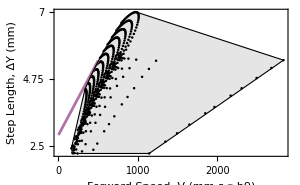

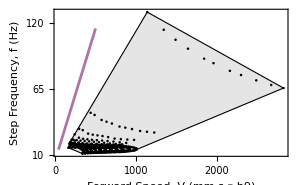

```mathematica
relations=speedRelation[7,100];
p05Ca1=plotfuncComp[relations[[1]],{2.5,4.75,7},{0,1000,2000},"Step Length, ΔY (mm)","Forward Speed, V (mm s ⁻.b9)",cataglyphisAlbicansStride,{t,0,500}]
p05Ca2=plotfuncComp[relations[[2]],{10,65,120},{0,1000,2000},"Step Frequency, f (Hz)","Forward Speed, V (mm s ⁻.b9)",cataglyphisAlbicansFreq,{t,40,500}]
```

```mathematica
closedranges[relations[[2]],relations[[1]],cataglyphisAlbicansFreq,cataglyphisAlbicansStride,20]
```

{{53.4569,68.8036},{0.467647,1.96671},{161.828,239.456},{16.089,27.172},{365.702,673.024},{4.61101,6.15334}}

### Cataglyphis Fortis

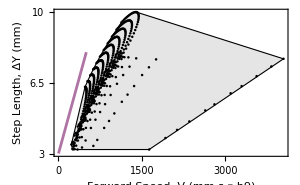

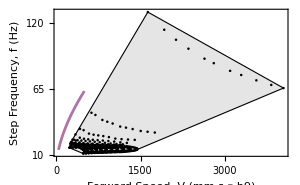

```mathematica
relations=speedRelation[10,100];
p05Cf1=plotfuncComp[relations[[1]],{3,6.5,10},{0,1500,3000},"Step Length, ΔY (mm)","Forward Speed, V (mm s ⁻.b9)",cataglyphisFortisStride,{t,0,500}]
p05Cf2=plotfuncComp[relations[[2]],{10,65,120},{0,1500,3000},"Step Frequency, f (Hz)","Forward Speed, V (mm s ⁻.b9)",cataglyphisFortisFreq,{t,40,500}]
```

```mathematica
closedranges[relations[[2]],relations[[1]],cataglyphisFortisFreq,cataglyphisFortisStride,20]
```

{{1.65809,60.8147},{19.0499,35.074},{231.182,1921.81},{16.1113,129.363},{231.182,579.639},{3.46432,6.89046}}

### Formica Polyctena

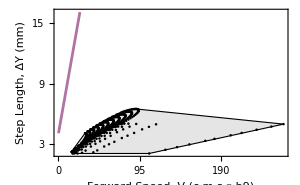

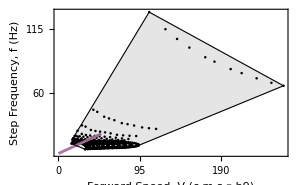

```mathematica
relations=speedRelation[6.5,100];
p05fp1=plotfuncComp[{#[[1]]/10,#[[2]]}&/@relations[[1]],{3,9,15},{0,95,190},"Step Length, ΔY (mm)","Forward Speed, V (c m s ⁻.b9)",formicaPolyctenaStride,{t,0,25}]
p05fp2=plotfuncComp[{#[[1]]/10,#[[2]]}&/@relations[[2]],{5,60,115},{0,95,190},"Step Frequency, f (Hz)","Forward Speed, V (c m s ⁻.b9)",formicaPolyctenaFreq,{t,0,50}]
```

```mathematica
closedranges[relations[[2]],relations[[1]],formicaPolyctenaFreq,formicaPolyctenaStride,20]
```

{{67.3412,78.0923},{97.046,97.8539},{150.269,222.352},{16.089,27.172},{150.269,207.31},{2.09499,2.62674}}

### Cataglyphis bombycina

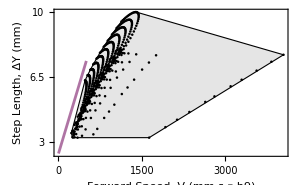

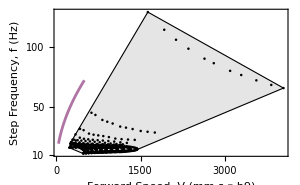

```mathematica
relations=speedRelation[10,100];
p05Cbm1=plotfuncComp[relations[[1]],{3,6.5,10},{0,1500,3000},"Step Length, ΔY (mm)","Forward Speed, V (mm s ⁻.b9)",cataglyphisBombycinaStride,{t,0,500}]
p05Cbm2=plotfuncComp[relations[[2]],{10,50,100},{0,1500,3000},"Step Frequency, f (Hz)","Forward Speed, V (mm s ⁻.b9)",cataglyphisBombycinaFreq,{t,40,500}]
```

```mathematica
closedranges[relations[[2]],relations[[1]],cataglyphisBombycinaFreq,cataglyphisBombycinaStride,20]
```

{{3.36383,67.3626},{11.5591,26.1954},{231.182,1921.81},{16.1113,129.363},{231.182,579.639},{3.46432,6.89046}}

## y 0

### Code

```mathematica
mV=Table[i,{i,0.1,1,0.02}];
nE2=Length[mV];


l0V=Table[i,{i,0,1,0.1}];
nE3=Length[l0V];
```

```mathematica
Clear[sol,fulsol,dsol,yf,tDe,yDe,yPDe,vDe,sgnvDe,p0De,parameters,intime,trfa,times,tgrps,fk,fb,l0,ldev,kk,b,m,speedD,leq,mV,bV,stepfreq,steplength,energy];

nE=1;

Subscript[yf, 1]=1;
Subscript[tDe, 1]=0;
Subscript[yDe, 1]=0;
Subscript[yPDe, 1]=0;



period=200Pi;

Table[Table[{parameters={l0->l0V[[nldev]],ϕ->mV[[nm]]},


Table[{Subscript[leq, k][t]=l0- Cos[ (t-Subscript[tDe, k])],
Subscript[fk, k][t]=(Subscript[leq, k][t]-(y[t]-Subscript[yf, k])),
solutions={};
seeds=Table[i,{i,Subscript[tDe, k]+2,Subscript[tDe, k]+period,2}];
Subscript[sol, k]=NDSolve[Evaluate[{y''[t]==ϕ^2  Subscript[fk, k][t],y[Subscript[tDe, k]]==Subscript[yDe, k],y'[Subscript[tDe, k]]==Subscript[yPDe, k]}/.parameters],y[t],{t,Subscript[tDe, k],Subscript[tDe, k]+period}],
Subscript[fulsol, k]=(y[t]/. Subscript[sol, k])[[1]],
Subscript[dsol, k]=D[Subscript[fulsol, k],t],
Subscript[ddsol, k]=D[Subscript[dsol, k],t],
i=1,
While[Length[solutions]<20&&i<Length[seeds],
sol2=Quiet@FindRoot[Subscript[dsol, k]==Subscript[yPDe, k],{t,seeds[[i]]}];
If[Not[Head[sol2]===FindRoot],AppendTo[solutions,sol2]];
i++;
],

times=Select[t/.solutions,(Subscript[tDe, k]+2)<#<(Subscript[tDe, k]+period)&],
ys=Flatten[(Subscript[dsol, k]/.t->times)],
tf=Table[(ys[[i]]-Subscript[yPDe, k])<10^-6,{i,1,Length[ys]}],

Subscript[tDe, k+1]=Min[DeleteDuplicates[Pick[times,tf]]];
Subscript[yDe, k+1]=Chop[Subscript[fulsol, k]/.t->Subscript[tDe, k+1]/.parameters],
Subscript[yPDe, k+1]=Chop[(Subscript[dsol, k])/.t->Subscript[tDe, k+1]/.parameters],

Subscript[yf, k+1]=Subscript[yf, k]+(Subscript[yDe, k+1]-Subscript[yDe, k])}


,{k,1,nE}],
Subscript[speedD, nm,nldev]=(Subscript[yDe, nE+1]-Subscript[yDe, 1])/Subscript[tDe, nE+1],
Subscript[stepfreq, nm,nldev]=1/{Subscript[tDe, nE+1]-Subscript[tDe, nE]},
Subscript[steplength, nm,nldev]=Subscript[yDe, nE+1]-Subscript[yDe, nE],
Subscript[energy, nm,nldev]=NIntegrate[Abs[(Subscript[leq, nE][t]-(Subscript[fulsol, nE]-Subscript[yf, nE]))(D[Subscript[leq, nE][t],t])/.parameters],{t,Subscript[tDe, nE],Subscript[tDe, nE+1]},PrecisionGoal->3],
Subscript[grf, nm,nldev]=Max[First[FindMaximum[(Subscript[leq, nE][t]-(Subscript[fulsol, nE]-Subscript[yf, nE]))/.parameters,{t,Subscript[tDe, nE],Subscript[tDe, nE+1]}]],
Abs[First[FindMinimum[(Subscript[leq, nE][t]-(Subscript[fulsol, nE]-Subscript[yf, nE]))/.parameters,{t,Subscript[tDe, nE+1],Subscript[tDe, nE]}]]]]

},{nm,1,nE2}],{nldev,1,nE3}];
```

InterpolatingFunction::dmval: Input value {-0.0787636} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.127442} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.206206} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
tdata=Table[i,{i,0,1,1/(4-1)}];
tydata=Table[i,{i,0,1,1/(3-1)}];
mjtkxdata=Table[i,{i,Min[mV],Max[mV],(Max[mV]-Min[mV])/(4-1)}];

ticksx=Table[{tdata[[Position[mjtkxdata,i][[1,1]]]],i,0.02},{i,mjtkxdata}];
mjtkx=Join[{ticksx[[1]]},Round[Rest[Most[ticksx]],0.01],{Round[Last[ticksx],0.01]}];


mjtkydata=Table[i,{i,Min[l0V],Max[l0V],(Max[l0V]-Min[l0V])/(3-1)}];


ticksy=Table[{tydata[[Position[mjtkydata,i][[1,1]]]],i,0.02},{i,mjtkydata}];
mjtky=Join[{ticksy[[1]]},Round[Rest[Most[ticksy]],0.01],{Round[Last[ticksy],0.01]}];

mtk=Table[{i,"",0.01},{i,0,1,1/(9-1)}];


speed=Table[Table[Subscript[speedD, nm,nldev],{nm,1,nE2}],{nldev,1,nE3}];
steplengthD=Table[Table[Subscript[steplength, nm,nldev]*2,{nm,1,nE2}],{nldev,1,nE3}];
stepfreqD=Table[Flatten[Table[Subscript[stepfreq, nm,nldev]/2,{nm,1,nE2}]],{nldev,1,nE3}];
energyD=Table[Flatten[Table[Subscript[energy, nm,nldev],{nm,1,nE2}]],{nldev,1,nE3}];
gRFmax=Table[Flatten[Table[Subscript[grf, nm,nldev],{nm,1,nE2}]],{nldev,1,nE3}];
effic=0.5 speed^2/energyD*100;
cot=energyD/steplengthD;
```

### import export

```mathematica
Export["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Code2\\1D model\\speedY0.mx",speed];
Export["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Code2\\1D model\\steplengthDY0.mx",steplengthD];
Export["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Code2\\1D model\\stepfreqDY0.mx",stepfreqD];
Export["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Code2\\1D model\\energyDY0.mx",energyD];
Export["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Code2\\1D model\\grfmaxY0.mx",gRFmax];
Export["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Code2\\1D model\\efficY0.mx",effic];
Export["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Code2\\1D model\\cotY0.mx",cot];
```

```mathematica
speed=Import["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Code2\\1D model\\speedY0.mx"];
steplengthD=Import["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Code2\\1D model\\steplengthDY0.mx"];
stepfreqD=Import["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Code2\\1D model\\stepfreqDY0.mx"];
energyD=Import["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Code2\\1D model\\energyDY0.mx"];
gRFmax=Import["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Code2\\1D model\\grfmaxY0.mx"];
effic=Import["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Code2\\1D model\\efficY0.mx"];
cot=Import["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Code2\\1D model\\cotY0.mx"];
```

### Cataglyphis Bicolor

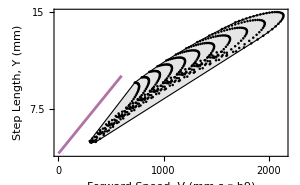

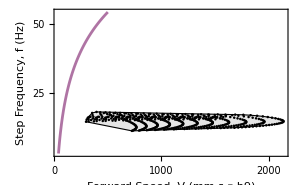

```mathematica
relations=speedRelation[15,100];
p0Cb1=plotfuncComp[relations[[1]],{0,7.5,15},{0,1000,2000},"Step Length, Y (mm)","Forward Speed, V (mm s ⁻.b9)",cataglyphisBicolorStride,{t,0,600}]
p0Cb2=plotfuncComp[relations[[2]],{0,25,50},{0,1000,2000},"Step Frequency, f (Hz)","Forward Speed, V (mm s ⁻.b9)",cataglyphisBicolorFreq,{t,40,500}]
```

```mathematica
closedranges[relations[[2]],relations[[1]],cataglyphisBicolorFreq,cataglyphisBicolorStride,200]
```

{{62.6855,82.3209},{15.7542,34.8758},{297.015,1086.06},{11.1274,18.0045},{297.015,1157.95},{4.92476,11.8432}}

### Cataglyphis Albicans

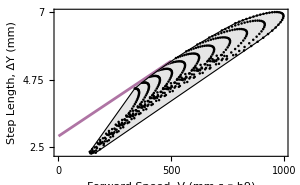

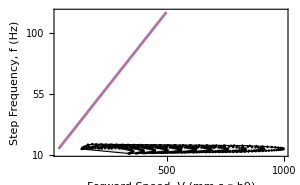

```mathematica
relations=speedRelation[7,100];
p0Ca1=plotfuncComp[relations[[1]],{2.5,4.75,7},{0,500,1000},"Step Length, ΔY (mm)","Forward Speed, V (mm s ⁻.b9)",cataglyphisAlbicansStride,{t,0,500}]
p0Ca2=plotfuncComp[relations[[2]],{10,55,100},{0,500,1000},"Step Frequency, f (Hz)","Forward Speed, V (mm s ⁻.b9)",cataglyphisAlbicansFreq,{t,40,500}]
```

```mathematica
closedranges[relations[[2]],relations[[1]],cataglyphisAlbicansFreq,cataglyphisAlbicansStride,20]
```

{{57.9973,66.958},{0.161249,1.53924},{138.607,190.736},{14.4422,18.0045},{369.295,668.835},{4.6488,6.15188}}

### Cataglyphis Fortis

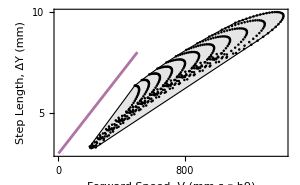

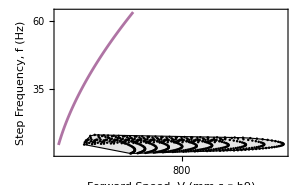

```mathematica
relations=speedRelation[10,100];
p0Cf1=plotfuncComp[relations[[1]],{0,5,10},{0,800,1600},"Step Length, ΔY (mm)","Forward Speed, V (mm s ⁻.b9)",cataglyphisFortisStride,{t,0,500}]
p0Cf2=plotfuncComp[relations[[2]],{35,10,60},{0,800,1600},"Step Frequency, f (Hz)","Forward Speed, V (mm s ⁻.b9)",cataglyphisFortisFreq,{t,40,500}]
```

```mathematica
closedranges[relations[[2]],relations[[1]],cataglyphisFortisFreq,cataglyphisFortisStride,20]
```

{{56.7013,65.1071},{18.9004,34.517},{198.01,286.374},{14.4422,18.0045},{198.01,540.054},{3.29976,6.65323}}

### Formica Polyctena

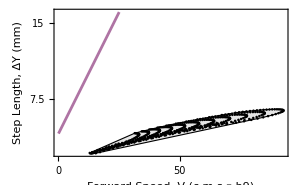

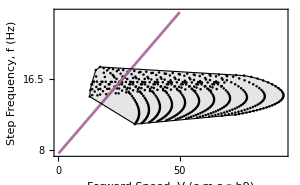

```mathematica
relations=speedRelation[6.5,100];
p0fp1=plotfuncComp[{#[[1]]/10,#[[2]]}&/@relations[[1]],{0,7.5,15},{0,50,100},"Step Length, ΔY (mm)","Forward Speed, V (c m s ⁻.b9)",formicaPolyctenaStride,{t,0,25}]
p0fp2=plotfuncComp[{#[[1]]/10,#[[2]]}&/@relations[[2]],{8,16.5,25},{0,50,100},"Step Frequency, f (Hz)","Forward Speed, V (c m s ⁻.b9)",formicaPolyctenaFreq,{t,0,50}]
```

```mathematica
closedranges[relations[[2]],relations[[1]],formicaPolyctenaFreq,formicaPolyctenaStride,20]
```

{{70.4154,77.7298},{96.6801,97.3687},{128.707,172.957},{14.4422,18.0045},{128.707,172.957},{2.13406,2.54931}}

### Cataglyphis Bombycina

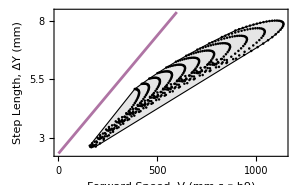

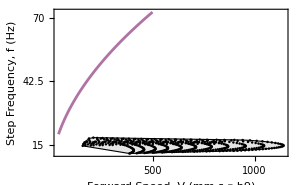

```mathematica
relations=speedRelation[8,100];
p0Cbm1=plotfuncComp[relations[[1]],{3,5.5,8},{0,500,1000},"Step Length, ΔY (mm)","Forward Speed, V (mm s ⁻.b9)",cataglyphisBombycinaStride,{t,0,600}]
p0Cbm2=plotfuncComp[relations[[2]],{15,42.5,70},{0,500,1000},"Step Frequency, f (Hz)","Forward Speed, V (mm s ⁻.b9)",cataglyphisBombycinaFreq,{t,40,500}]
```

```mathematica
closedranges[relations[[2]],relations[[1]],cataglyphisBombycinaFreq,cataglyphisBombycinaStride,200]
```

{{59.6228,83.6373},{18.1712,37.4817},{158.408,544.615},{11.1274,18.0045},{158.408,617.572},{2.62654,6.31635}}

## Combined Plots

```mathematica
Needs["MaTeX`"]
```

```mathematica
plot=Show[GraphicsGrid[{{p5Ca1,p1Ca1,p05Ca1,p0Ca1},{p5Cb1,p1Cb1,p05Cb1,p0Cb1},{p5Cbm1,p1Cbm1,p05Cbm1,p0Cbm1},{p5Cf1,p1Cf1,p05Cf1,p0Cf1},{p5fp1,p1fp1,p05fp1,p0fp1}},ImageSize->{1300,1400}],
Graphics[{
Text[Style[Rotate[MaTeX["\\LARGE \\textit{C. albicans}"],Pi/2],18],{-20,-120}],
Text[Style[Rotate[MaTeX["\\LARGE \\textit{C. bicolor}"],Pi/2],18],{-20,-400}],
Text[Style[Rotate[MaTeX["\\LARGE \\textit{C. bombycina}"],Pi/2],18],{-20,-680}],
Text[Style[Rotate[MaTeX["\\LARGE \\textit{C. fortis}"],Pi/2],18],{-20,-960}],
Text[Style[Rotate[MaTeX["\\LARGE \\textit{F. polyctena}"],Pi/2],18],{-20,-1250}],
Text[Style[MaTeX["\\LARGE \\text{$\\dot{y}_0=0.5$}"],18],{180,0}],
Text[Style[MaTeX["\\LARGE \\text{$\\dot{y}_0=0.1$}"],18],{500,0}],
Text[Style[MaTeX["\\LARGE \\text{$\\dot{y}_0=0.05$}"],18],{820,0}],
Text[Style[MaTeX["\\LARGE \\text{$\\dot{y}_0=0$}"],18],{1150,0}],
Text[Style["a",18,FontFamily->"Latin Modern Math"],{20,-10}],
Text[Style["b",18,FontFamily->"Latin Modern Math"],{350,-10}],
Text[Style["c",18,FontFamily->"Latin Modern Math"],{670,-10}],
Text[Style["d",18,FontFamily->"Latin Modern Math"],{1000,-10}],
Text[Style["e",18,FontFamily->"Latin Modern Math"],{20,-280}],
Text[Style["f",18,FontFamily->"Latin Modern Math"],{350,-280}],
Text[Style["g",18,FontFamily->"Latin Modern Math"],{670,-280}],
Text[Style["h",18,FontFamily->"Latin Modern Math"],{1000,-280}],
Text[Style["i",18,FontFamily->"Latin Modern Math"],{20,-550}],
Text[Style["j",18,FontFamily->"Latin Modern Math"],{350,-550}],
Text[Style["k",18,FontFamily->"Latin Modern Math"],{670,-550}],
Text[Style["l",18,FontFamily->"Latin Modern Math"],{1000,-550}],
Text[Style["m",18,FontFamily->"Latin Modern Math"],{20,-850}],
Text[Style["n",18,FontFamily->"Latin Modern Math"],{350,-850}],
Text[Style["o",18,FontFamily->"Latin Modern Math"],{670,-850}],
Text[Style["p",18,FontFamily->"Latin Modern Math"],{1000,-850}],
Text[Style["q",18,FontFamily->"Latin Modern Math"],{20,-1120}],
Text[Style["r",18,FontFamily->"Latin Modern Math"],{350,-1120}],
Text[Style["s",18,FontFamily->"Latin Modern Math"],{670,-1120}],
Text[Style["t",18,FontFamily->"Latin Modern Math"],{1000,-1120}]

}]

]
```

-Graphics-

```mathematica
Export["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Figures\\1DValidA.pdf",plot]
```

C:\Users\by2475\Dropbox\NYU POSTDOC DRIVE\Ants Project\Mathematica\2D model\Updated Figures\1DValidA.pdf

```mathematica
plot2=Show[GraphicsGrid[{{p5Ca2,p1Ca2,p05Ca2,p0Ca2},{p5Cb2,p1Cb2,p05Cb2,p0Cb2},{p5Cbm2,p1Cbm2,p05Cbm2,p0Cbm2},{p5Cf2,p1Cf2,p05Cf2,p0Cf2},{p5fp2,p1fp2,p05fp2,p0fp2}},ImageSize->{1350,1400}],
Graphics[{
Text[Style[Rotate[MaTeX["\\LARGE \\textit{C. albicans}"],Pi/2],18],{-20,-120}],
Text[Style[Rotate[MaTeX["\\LARGE \\textit{C. bicolor}"],Pi/2],18],{-20,-400}],
Text[Style[Rotate[MaTeX["\\LARGE \\textit{C. bombycina}"],Pi/2],18],{-20,-680}],
Text[Style[Rotate[MaTeX["\\LARGE \\textit{C. fortis}"],Pi/2],18],{-20,-960}],
Text[Style[Rotate[MaTeX["\\LARGE \\textit{F. polyctena}"],Pi/2],18],{-20,-1250}],
Text[Style[MaTeX["\\LARGE \\text{$\\dot{y}_0=0.5$}"],18],{180,0}],
Text[Style[MaTeX["\\LARGE \\text{$\\dot{y}_0=0.1$}"],18],{500,0}],
Text[Style[MaTeX["\\LARGE \\text{$\\dot{y}_0=0.05$}"],18],{820,0}],
Text[Style[MaTeX["\\LARGE \\text{$\\dot{y}_0=0$}"],18],{1150,0}],
Text[Style["a",18,FontFamily->"Latin Modern Math"],{20,-10}],
Text[Style["b",18,FontFamily->"Latin Modern Math"],{350,-10}],
Text[Style["c",18,FontFamily->"Latin Modern Math"],{670,-10}],
Text[Style["d",18,FontFamily->"Latin Modern Math"],{1000,-10}],
Text[Style["e",18,FontFamily->"Latin Modern Math"],{20,-280}],
Text[Style["f",18,FontFamily->"Latin Modern Math"],{350,-280}],
Text[Style["g",18,FontFamily->"Latin Modern Math"],{670,-280}],
Text[Style["h",18,FontFamily->"Latin Modern Math"],{1000,-280}],
Text[Style["i",18,FontFamily->"Latin Modern Math"],{20,-550}],
Text[Style["j",18,FontFamily->"Latin Modern Math"],{350,-550}],
Text[Style["k",18,FontFamily->"Latin Modern Math"],{670,-550}],
Text[Style["l",18,FontFamily->"Latin Modern Math"],{1000,-550}],
Text[Style["m",18,FontFamily->"Latin Modern Math"],{20,-850}],
Text[Style["n",18,FontFamily->"Latin Modern Math"],{350,-850}],
Text[Style["o",18,FontFamily->"Latin Modern Math"],{670,-850}],
Text[Style["p",18,FontFamily->"Latin Modern Math"],{1000,-850}],
Text[Style["q",18,FontFamily->"Latin Modern Math"],{20,-1120}],
Text[Style["r",18,FontFamily->"Latin Modern Math"],{350,-1120}],
Text[Style["s",18,FontFamily->"Latin Modern Math"],{670,-1120}],
Text[Style["t",18,FontFamily->"Latin Modern Math"],{1000,-1120}]

}]

]
```

-Graphics-

```mathematica
Export["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Figures\\1DValidB.pdf",plot2]
```

C:\Users\by2475\Dropbox\NYU POSTDOC DRIVE\Ants Project\Mathematica\2D model\Updated Figures\1DValidB.pdf